```mathematica
SocialMediaData["Twitter", "FollowerNetwork"]
```

SocialMediaData::lim: Rate limit exceeded. Use SocialMediaData["Twitter", "RateLimit"] for current rate limits.

SocialMediaData[Twitter,FollowerNetwork]

```mathematica
SocialMediaData["Facebook", "FriendNetwork"]
```

-Graphics-

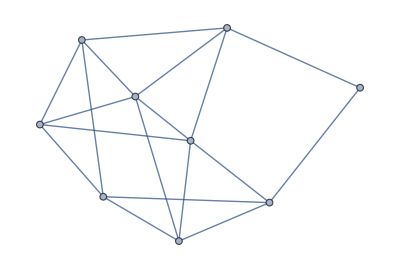

```mathematica
RandomGraph[WattsStrogatzGraphDistribution[9, 0.3, 2]]
```

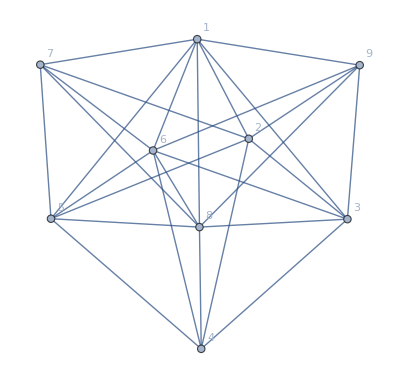

```mathematica
Show[SetProperty[%20,VertexLabels->"Name"],PlotRange->All]
```

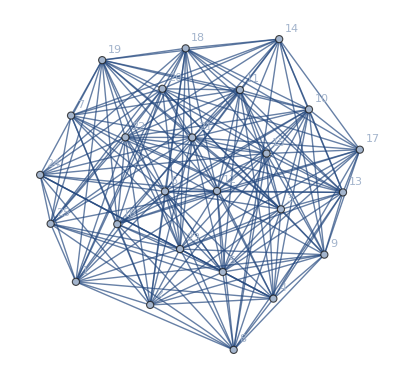

```mathematica
Show[SetProperty[%17,VertexLabels->"Name"],PlotRange->All]
```

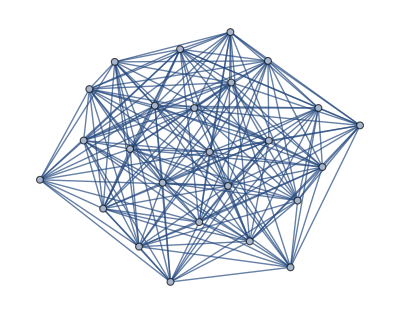

Set::write: Tag Inherited in Inherited[State] is Protected.

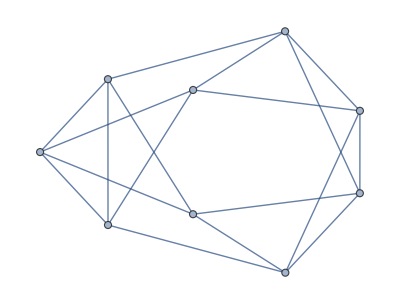

```mathematica
RandomGraph[DegreeGraphDistribution[Table[4, 9]]]
```

```mathematica
AdjacencyMatrix[%37]
```

SparseArray[<36>, {9, 9}]

```mathematica
Normal[%38]
```

{{0,1,0,1,0,0,0,1,1},{1,0,1,1,0,0,1,0,0},{0,1,0,0,1,1,0,1,0},{1,1,0,0,0,0,1,0,1},{0,0,1,0,0,1,1,0,1},{0,0,1,0,1,0,1,1,0},{0,1,0,1,1,1,0,0,0},{1,0,1,0,0,1,0,0,1},{1,0,0,1,1,0,0,1,0}}

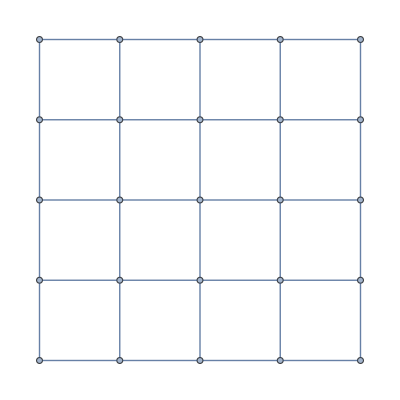

```mathematica
g = GridGraph[{5,5}]
```

```mathematica
updateIGraphM[]:=Module[{json,download,target,msg},Check[json=Import["https://api.github.com/repos/szhorvat/IGraphM/releases","JSON"];
download=Lookup[First@Lookup[First[json],"assets"],"browser_download_url"];
msg="Downloading IGraph/M "<>Lookup[First[json],"tag_name"]<>" ...";
target=FileNameJoin[{CreateDirectory[],"IGraphM.paclet"}];
If[$Notebooks,PrintTemporary@Labeled[ProgressIndicator[Appearance->"Necklace"],msg,Right],Print[msg]];
URLSave[download,target],Return[$Failed]];
If[FileExistsQ[target],PacletManager`PacletInstall[target],$Failed]]
```

```mathematica
updateIGraphM[]
```

```mathematica
Needs["PacletManager`"]
PacletInstall["\\\\ad.ucl.ac.uk\\homeh\\zcabhkh\\Documents\\IGraphM-0.3.97.2.paclet"]
```

PacletInstall::samevers: A paclet named IGraphM with the same version number (0.3.97.2) is already installed. Use PacletUninstall to remove the existing version first, or call PacletInstall with IgnoreVersion->True.

$Failed

```mathematica
PacletFind["IGraphM"]
```

{Paclet[IGraphM,0.3.97.2,<>]}

```mathematica
PacletUninstall["IGraphM"]
```

PacletManager[]

```mathematica
<<IGraphM`
```

LibraryFunction::notfound: Symbol libwinpthread-1 not found.

LibraryFunction::notfound: Symbol libgcc_s_seh-1 not found.

LibraryFunction::notfound: Symbol libstdc++-6 not found.

General::stop: Further output of LibraryFunction::notfound will be suppressed during this calculation.

Loading failed, trying to recompile ...

Recompile::build: No build settings found. Please check BuildSettings.m.

Cannot load or compile library. \[FreakedSmiley] Aborting.

$Aborted

```mathematica
IGraphM[]
```

IGraphM[]

```mathematica
?IGRewireEdges
```

IGRewireEdges[graph, p] rewires each edge of the graph with probability p. Weights and other graph properties are discarded.
IGRewireEdges[graph, p, "In"] rewires the starting point of each edge with probability p. The in-degree sequence is preserved.
IGRewireEdges[graph, p, "Out"] rewires the endpoint of each edge with probability p. The out-degree sequence is preserved.

```mathematica
g
coords = GraphEmbedding[g]
```

-Graphics-

{{1.,1.},{1.,2.},{1.,3.},{1.,4.},{1.,5.},{2.,1.},{2.,2.},{2.,3.},{2.,4.},{2.,5.},{3.,1.},{3.,2.},{3.,3.},{3.,4.},{3.,5.},{4.,1.},{4.,2.},{4.,3.},{4.,4.},{4.,5.},{5.,1.},{5.,2.},{5.,3.},{5.,4.},{5.,5.}}

```mathematica
Graph[IGRewireEdges[g, 0.3], VertexCoordinates-> coords]
```

Graph[IGRewireEdges[-Graphics-,0.3],VertexCoordinates→{{1.,1.},{1.,2.},{1.,3.},{1.,4.},{1.,5.},{2.,1.},{2.,2.},{2.,3.},{2.,4.},{2.,5.},{3.,1.},{3.,2.},{3.,3.},{3.,4.},{3.,5.},{4.,1.},{4.,2.},{4.,3.},{4.,4.},{4.,5.},{5.,1.},{5.,2.},{5.,3.},{5.,4.},{5.,5.}}]

```mathematica
<< IGraphM`
```

LibraryFunction::notfound: Symbol libwinpthread-1 not found.

LibraryFunction::notfound: Symbol libgcc_s_seh-1 not found.

LibraryFunction::notfound: Symbol libstdc++-6 not found.

General::stop: Further output of LibraryFunction::notfound will be suppressed during this calculation.

Loading failed, trying to recompile ...

Recompile::build: No build settings found. Please check BuildSettings.m.

Cannot load or compile library. \[FreakedSmiley] Aborting.

$Aborted

```mathematica
IGraphM`Developer`GetInfo[]
```

IGraphM`Developer`GetInfo[]

```mathematica
$UserBaseDirectory
```

C:\Users\zcabhkh\AppData\Roaming\Mathematica